# Mu3e sensitivity to low-mass boson

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"madevent-analysis.nb"}]]
```

These will be set from the outside when called from analyze-all

```mathematica
(*rundir="run_300";
sig=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events",rundir,"unweighted_events.lhe.gz"}];
bkg=FileNameJoin[{NotebookDirectory[],"..","muon-decay-background","Events",rundir,"unweighted_events.lhe.gz"}];*)
rawSig=Import[sig,"Table"];
rawBkg=Import[bkg,"Table"];
sigEvents=ReadME[rawSig];
bkgEvents=ReadME[rawBkg];
```

Define some useful functions

```mathematica
GetRate[raw_]:=
(
posStart=Position[raw,{"<init>"}][[1,1]];
posEnd=Position[raw,{"</init>"}][[1,1]];
DeleteCases[Take[raw,{posStart,posEnd}],{"<init>"}|{"</init>"}][[2,1]]*1
);

InvMass[event_,pair_]:=Sqrt[2*(enOf[event[[pair[[1]]]]]*enOf[event[[pair[[2]]]]]-ThreeVectorFrom[event[[pair[[1]]]]].ThreeVectorFrom[event[[pair[[2]]]]])];
ScaleData[bins_,counts_,scale_]:=
(
(* Note: scale must be an integer *)
Inner[ConstantArray, bins, scale*Append[counts, 0], Join]
)
```

The last event is just a set of headers, so we should ignore it with regards to our events.

```mathematica
Nsig=Length[sigEvents]-1;
Nbkg=Length[bkgEvents]-1;
(*EventPrint/@{sigEvents[[1]],bkgEvents[[1]]};*)
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
μ^+ | in | 0 | 0 | 0 | 0 | 0. | 0. | 1.×10^-14 | 0.10566 | 0.10566 | 0. | 1.
e^+ | out | 3 | 3 | 0 | 0 | 0.00970535 | -0.00565767 | 0.0449326 | 0.0463185 | 0.000511 | 0. | 1.
ϕ | decayed | 1 | 0 | 0 | 0 | -0.0026182 | 0.00855666 | 0.0202887 | 0.0773265 | 0.0740789 | 0. | 0.
e^- | out | 3 | 3 | 0 | 0 | -0.0123236 | 0.0142143 | -0.0246439 | 0.0310081 | 0.000511 | 0. | 1.
e^+ | out | 1 | 0 | 0 | 0 | 0.000559813 | -0.00276034 | 0.0008228 | 0.00297842 | 0.000511 | 0. | 1.
⋁_e  | out | 1 | 0 | 0 | 0 | -0.00499016 | -0.000451593 | -0.00573304 | 0.00761403 | 0. | 0. | -1.
(⋁_μ)^c | out | 1 | 0 | 0 | 0 | 0.00704856 | -0.00534473 | -0.0153784 | 0.017741 | 0. | 0. | 1.)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
μ^+ | in | 0 | 0 | 0 | 0 | 0. | 0. | 1.×10^-14 | 0.10566 | 0.10566 | 0. | 1.
e^+ | out | 1 | 0 | 0 | 0 | -0.0305852 | 0.00690716 | 0.0136769 | 0.0342124 | 0.000511 | 0. | 1.
e^+ | out | 1 | 0 | 0 | 0 | 0.00162445 | 0.000472529 | -0.000531301 | 0.00184541 | 0.000511 | 0. | 1.
e^- | out | 1 | 0 | 0 | 0 | -0.00710441 | -0.00494103 | 0.00121285 | 0.0087532 | 0.000511 | 0. | -1.
⋁_e  | out | 1 | 0 | 0 | 0 | 0.0372637 | -0.0189945 | -0.00596622 | 0.0422489 | 0. | 0. | -1.
(⋁_μ)^c | out | 1 | 0 | 0 | 0 | -0.00119852 | 0.0165559 | -0.00839226 | 0.0186001 | 0. | 0. | 1.)

We are only really interested in the outgoing particles.

```mathematica
sigEvents=SetOut[sigEvents];
bkgEvents=SetOut[bkgEvents];
```

Construct the invariant masses of the electron-positron pairs.

```mathematica
firstPair=InvMass[#,{1,2}]&/@sigEvents[[1;;Nsig]];
secondPair=InvMass[#,{2,3}]&/@sigEvents[[1;;Nsig]];
sigInvMasses=Join[firstPair,secondPair];
sigRate=GetRate[rawSig];

firstPair=InvMass[#,{1,2}]&/@bkgEvents[[1;;Nbkg]];
secondPair=InvMass[#,{2,3}]&/@bkgEvents[[1;;Nbkg]];
bkgInvMasses=Join[firstPair,secondPair];
bkgRate=GetRate[rawBkg];
```

Histograms of the invariant mass spectrum of e^+e^- pairs
Note: We don’t have the histograms properly weighted yet!

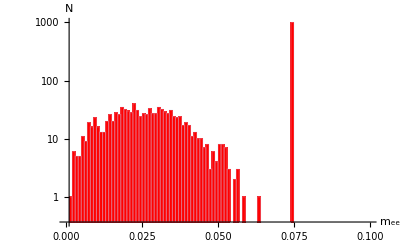

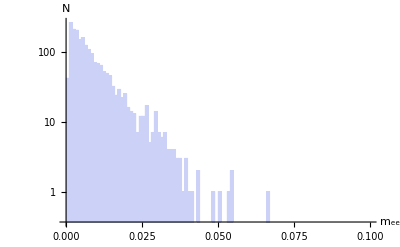

```mathematica
Histogram[sigInvMasses,{0,0.1,0.001},ScalingFunctions->"Log",AxesLabel->{"m_ee","N"},ChartStyle->Red]
Histogram[bkgInvMasses,{0,0.1,0.001},ScalingFunctions->"Log",AxesLabel->{"m_ee","N"}]
```

Compute the weight of each dataset

```mathematica
stopRate=2 10^9;
runTime=1;
Nstop=stopRate*runTime;
muonWidth=3.008/10^19;
sigBR=sigRate / (muonWidth+sigRate+bkgRate);
bkgBR=bkgRate/(muonWidth+sigRate+bkgRate);
sigScaling=Nstop*sigBR /Nsig;
bkgScaling=Nstop*bkgBR /Nbkg;
```

Get the histogram bin values so we can rescale as necessary.

```mathematica
{sigBins,sigCounts}=HistogramList[sigInvMasses,{0,0.1,0.001},sigScaling*#2&];
{bkgBins,bkgCounts}=HistogramList[bkgInvMasses,{0,0.1,0.001},bkgScaling*#2&];
sigCounts=Append[sigCounts,0.0]/2; (* There is one fewer counts than bins, and we double count our ee pairs *)
bkgCounts=Append[bkgCounts,0.0]/2;
```

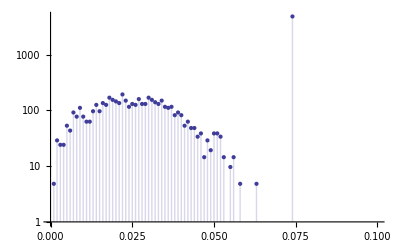

```mathematica
ListLogPlot[Transpose[{sigBins,sigCounts}],PlotRange->{{0,0.1},All},Filling->Axis]
```

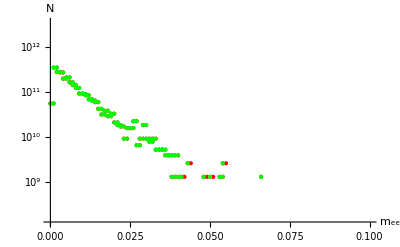

```mathematica
range={{0,0.1},{0.1*Min[DeleteCases[bkgCounts,0.0]],10*Max[bkgCounts]}};
ListLogPlot[{Transpose[{sigBins,sigCounts+bkgCounts}],Transpose[{bkgBins,bkgCounts}]},InterpolationOrder->0,PlotRange->range,PlotStyle->{Red,Green},Filling->{1->{2}},AxesLabel->{"m_ee","N"}]
```

Signal vs background computation

```mathematica
S=Total[sigCounts];
B=Total[bkgCounts];
sb=S/√B
```

0.00596489

Find if the number of signal events is larger than 3 statistical std. deviations of the background for any single bin

```mathematica
σ=√bkgCounts;
sigCounts;
3σ;
Or@@Flatten[Greater[#[[1]],#[[2]]]&/@Transpose[{sigCounts,3σ}]]
```

True